## <r^2(t)>, calcul numérique

### États propres dans la base atomique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
ClearAll[A,v,r];
A[i_,v_,r_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_,v_,r_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->A[i,v,r],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* états propres et leurs énergies dans la base atomique *)
valvec[v_,r_,i_]:=Eigensystem[h[i,v,r]]
```

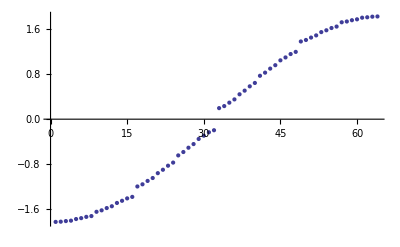

```mathematica
(* le spectre est bien comme on l'attend *)
ListPlot[Sort[valvec[.9,.9,6][[1]]]]
```

```mathematica
(* les vecteurs propres sont bien normalisés à 1 *)
Norm/@valvec[.1,.001,5][[2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
(* attention ! on fixe les couplages et la taille du système ! *)
Block[{n=5,v=0.9,r=0.9,val,vec,T,tmax=100,dt=10.,timelist,rmoy,d},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
d[i_]:=A[i,v,r];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
(* matrice T : propagateur*position *)
T=ParallelTable[Sum[d[k]*Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}],{t,timelist},{i,2^n},{j,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] Subscript[(T^*), ji] Subscript[T, ji] *)
rmoy=ParallelTable[Sum[Abs[T[[timeIt,j,i]]]^2,{j,2^n}],{timeIt,Length@timelist},{i,2^n}]
]
```

{{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231},{0.844231,0.847385,0.843073,0.850941,0.841489,0.846058,0.837842,0.858838,0.838485,0.836232,0.832618,0.841587,0.833289,0.837526,0.823576,0.860045,0.860045,0.823576,0.837526,0.833289,0.841587,0.832618,0.836232,0.838485,0.858838,0.837842,0.846058,0.841489,0.850941,0.843073,0.847385,0.844231}}